```mathematica
f[n_]:=a+b(n+1)+c(n+1)^(1/2)+d(n+1)^(1/4);
D[f[n],n]/.n->0
```

b+c/2+d/4

```mathematica
max=363056;
```

```mathematica
max^(1/2) *1//N
```

602.541

#### fix approach -> 602.541

{{a→-7.87318×10^-10,b→-7.87318×10^-10,c→1.}}

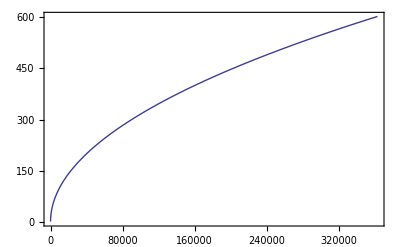

```mathematica
Solve[{a+b+c==1,a+max*b+max^(1/2) *c == 602.541,b+c/2==0.5},{a,b,c}]
Plot[(a+b(n+1)+c Sqrt[n+1])/.%,{n,0,max},Frame->True]
```

{{a→0.400665,b→0.000664958,c→0.59867}}

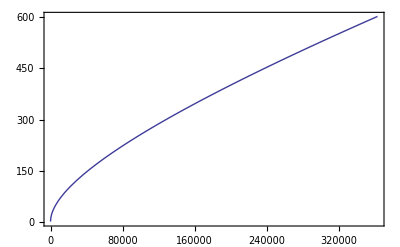

```mathematica
Solve[{a+b+c==1,a+max*b+max^(1/2) *c == 602.541,b+c/2==0.3},{a,b,c}]
Plot[(a+b(n+1)+c Sqrt[n+1])/.%,{n,0,max},Frame->True]
```

{{a→-0.400665,b→-0.000664959,c→1.40133}}

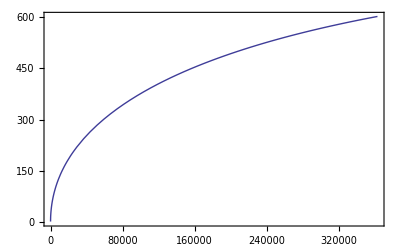

```mathematica
Solve[{a+b+c==1,a+max*b+max^(1/2) *c == 602.541,b+c/2==0.7},{a,b,c}]
Plot[(a+b(n+1)+c Sqrt[n+1])/.%,{n,0,max},Frame->True]
```

{{a→-0.80133,b→-0.00132992,c→1.80266}}

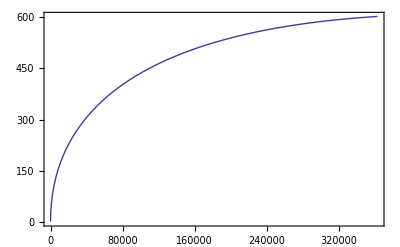

```mathematica
Solve[{a+b+c==1,a+max*b+max^(1/2) *c == 602.541,b+c/2==0.9},{a,b,c}]
Plot[(a+b(n+1)+c Sqrt[n+1])/.%,{n,0,max},Frame->True]
```

#### fix slope -> 0.5

{{a→0.0010984,b→0.0010984,c→0.997803}}

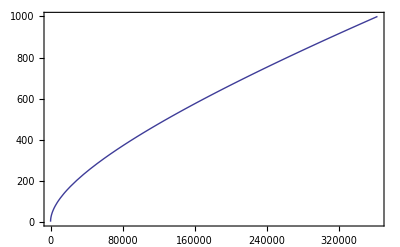

```mathematica
Solve[{a+b+c==1,a+max*b+max^(1/2) *c == 1000,b+c/2==0.5},{a,b,c}]
Plot[(a+b(n+1)+c Sqrt[n+1])/.%,{n,0,max},Frame->True]
```

{{a→0.00248018,b→0.00248018,c→0.99504}}

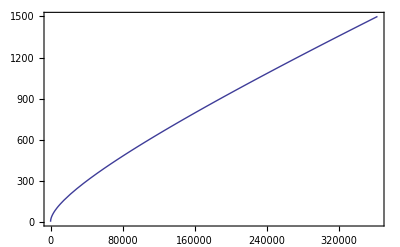

```mathematica
Solve[{a+b+c==1,a+max*b+max^(1/2) *c == 1500,b+c/2==0.5},{a,b,c}]
Plot[(a+b(n+1)+c Sqrt[n+1])/.%,{n,0,max},Frame->True]
```

{{a→0.00386196,b→0.00386196,c→0.992276}}

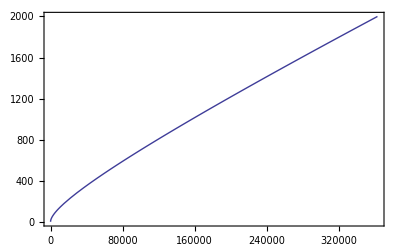

```mathematica
Solve[{a+b+c==1,a+max*b+max^(1/2) *c == 2000,b+c/2==0.5},{a,b,c}]
Plot[(a+b(n+1)+c Sqrt[n+1])/.%,{n,0,max},Frame->True]
```

{{a→0.0121526,b→0.0121526,c→0.975695}}

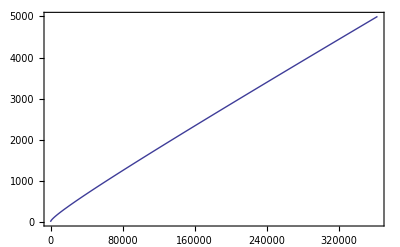

```mathematica
Solve[{a+b+c==1,a+max*b+max^(1/2) *c == 5000,b+c/2==0.5},{a,b,c}]
Plot[(a+b(n+1)+c Sqrt[n+1])/.%,{n,0,max},Frame->True]
```

```mathematica
Solve[{a+b+c==1,a+max*b+max^(1/2) *c == 10000,b+c/2==0.5},{a,b,c}]
```

{{a→0.0259705,b→0.0259705,c→0.948059}}